```mathematica
posData=<<"C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\PositionLog.txt";
```

```mathematica
centralIdealData=<<"C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\CentralIdealExpLog.txt";
```

```mathematica
centralNoisyData=<<"C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\CentralNoisyExpLog.txt";
```

```mathematica
CIAvgs=Mean[Rest@centralIdealData];
CISDevs=StandardDeviation[Rest@centralIdealData];
```

```mathematica
CNAvgs=Mean[Rest@centralNoisyData];
CNSDevs=StandardDeviation[Rest@centralNoisyData];
```

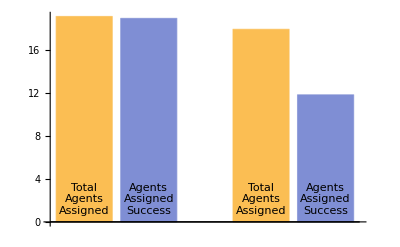

```mathematica
BarChart[{CIAvgs⟦2;;3⟧,CNAvgs⟦2;;3⟧},BarSpacing->{.15,1},ChartLabels->Placed[{"Total\nAgents\nAssigned","Agents\nAssigned\nSuccess"},Bottom]]
```

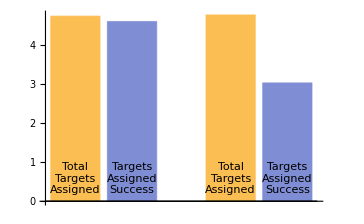

```mathematica
BarChart[{CIAvgs⟦4;;5⟧,CNAvgs⟦4;;5⟧},BarSpacing->{.15,1},ChartLabels->Placed[{"Total\nTargets\nAssigned","Targets\nAssigned\nSuccess"},Bottom]]
```